```mathematica
`Private`PainleveIIPositive["AS"] =`AblowitzSegurPositive`AblowitzSegurPositivePainleveII;
`Private`PainleveIIPositiveD["AS"] =`AblowitzSegurPositive`AblowitzSegurPositivePainleveIID;
Begin["`AblowitzSegurPositive`"];
```

## Negative x

```mathematica
θ[z_]:=I(4/3 z^3 + z);
x//Clear;
G//Clear;
s//Clear;
G[_,_][_?InfinityQ]:=IdentityMatrix[2];
G[{x_,s_},1][z_]=({{1, 0}, {ⅇ^(2 x^(3/2) θ[z]) s, 1}});
G[{x_,s_},6][z_]=({{1, - ⅇ^(-2  x^(3/2) θ[z]) s}, {0, 1}});
Gx[{x_,s_},1][z_]=({{0, 0}, {3 x^(1/2) θ[z] ⅇ^(2 x^(3/2) θ[z])  s, 0}});
Gx[{x_,s_},6][z_]=({{0, 3 x^(1/2)θ[z] ⅇ^(-2  x^(3/2) θ[z])  s}, {0, 0}});
```

```mathematica
M=6.;Cdefs[n_]:={Function[x,({{.5 I, -.5 I}, {x, -x}})],({{Line[{-M,M}], n}})};
Gl[{x_,s_}]:=({{G[{x,s},1], G[{x,s},6]}});
Glx[{x_,s_}]:=({{Gx[{x,s},1], Gx[{x,s},6]}});
n=70;slvr//Clear;slvr:=slvr=ScaledRHSolver[Cdefs[n]];
```

```mathematica
AblowitzSegurPositivePainleveII[s_,x_]:=-I/π Sqrt[x]Total[DomainIntegrate/@slvr[x,Gl[{x,-s}]]]⟦1,2⟧;
AblowitzSegurPositivePainleveIID[s_,x_]:=Module[{slvrx,Cm,Cp,Ul},
slvrx=slvr[x];
Cm=ScaledCauchyOperator[-1,slvrx];
Cp=ScaledCauchyOperator[1,slvrx];
Ul=slvrx[Gl[{x,-s}]];
I(-1/(π 2)x^(-1/2)Total[DomainIntegrate/@Ul]⟦1,2⟧-1/π Sqrt[x]((Cm[Ul]~FunListDot~ConstructCurve[Cdefs[n],Glx[{x,-s}],x]~FunListDot~(Inverse/@Cp[Ul])//DomainIntegrate))⟦1,2⟧)
]
```

## Tests

```mathematica
AblowitzSegurPositivePainleveIID[s  ,5.]-RiemannHilbert`Painleve`II`Private`PainleveIIDSmall[160,{s  ,0,-s},5.]
```

5.20417×10^-18+8.82107×10^-16 ⅈ

```mathematica
s=10.-1. I ;RiemannHilbert`Painleve`II`Private`PainleveIISmall[160,{s  ,0,-s},5.]-AblowitzSegurPositivePainleveII[s  ,5.]
```

-4.91415×10^-16-1.15034×10^-15 ⅈ

```mathematica
s=10.+1. I ;RiemannHilbert`Painleve`II`Private`PainleveIISmall[160,{s  ,0,-s},5.]-AblowitzSegurPositivePainleveII[s  ,5.]
```

2.13886×10^-16-1.08789×10^-15 ⅈ

```mathematica
s=10. ;RiemannHilbert`Painleve`II`Private`PainleveIISmall[160,{s  ,0,-s},5.]-AblowitzSegurPositivePainleveII[s  ,5.]
```

5.55095×10^-17-1.81886×10^-15 ⅈ

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[170,{1000. I ,0,-1000. I},5.]-AblowitzSegurPositivePainleveII[1000. I ,5.]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 19 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 964 »}, « 49 », « 964 »}
 may contain significant numerical errors.

1.13401×10^-10-2.93312×10^-11 ⅈ

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];
```

```mathematica
err//Clear;errD//Clear;
errD[k_]:=errD[k]=(data⟦k,4⟧-AblowitzSegurPositivePainleveIID[I,data⟦k,1⟧])/AblowitzSegurPositivePainleveIID[I,data⟦k,1⟧]//Abs;
err[k_]:=err[k]=(data⟦k,3⟧-AblowitzSegurPositivePainleveII[I,data⟦k,1⟧])/AblowitzSegurPositivePainleveII[I,data⟦k,1⟧]//Abs
```

```mathematica
data⟦650⟧
```

{0.5625,0.173819,-0.219727,0.224146,-1.74974,-1.51537,-1.49546}

```mathematica
err[650]
```

0.000950681

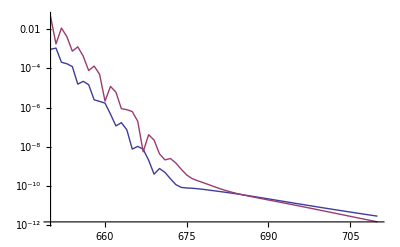

```mathematica
Monitor[TableLogPlot[{err[k],errD[k]},{k,650,710}],k]
```

### Test n and m

```mathematica
k=650;
```

```mathematica
M=6.;Cdefs[n_]:={Function[x,({{.5 I, -.5 I}, {x, -x}})],({{Line[{-M,M}], n}})};
Gl[{x_,s_}]:=({{G[{x,s},1], G[{x,s},6]}});
Glx[{x_,s_}]:=({{Gx[{x,s},1], Gx[{x,s},6]}});
n=70;slvr//Clear;slvr:=slvr=ScaledRHSolver[Cdefs[n]];
```

```mathematica
(data⟦k,3⟧-AblowitzSegurPositivePainleveII[I,data⟦k,1⟧])/AblowitzSegurPositivePainleveII[I,data⟦k,1⟧]
```

-0.000950681-4.92591×10^-18 ⅈ

```mathematica
M=6.;Cdefs[n_]:={Function[x,({{.5 I, -.5 I}, {x, -x}})],({{Line[{-M,M}], n}})};
Gl[{x_,s_}]:=({{G[{x,s},1], G[{x,s},6]}});
Glx[{x_,s_}]:=({{Gx[{x,s},1], Gx[{x,s},6]}});
n=100;slvr//Clear;slvr:=slvr=ScaledRHSolver[Cdefs[n]];
```

```mathematica
(data⟦k,3⟧-AblowitzSegurPositivePainleveII[I,data⟦k,1⟧])/AblowitzSegurPositivePainleveII[I,data⟦k,1⟧]
```

0.0000145643-4.58903×10^-17 ⅈ

```mathematica
M=6.;Cdefs[n_]:={Function[x,({{.5 I, -.5 I}, {x, -x}})],({{Line[{-M,M}], n}})};
Gl[{x_,s_}]:=({{G[{x,s},1], G[{x,s},6]}});
Glx[{x_,s_}]:=({{Gx[{x,s},1], Gx[{x,s},6]}});
n=200;slvr//Clear;slvr:=slvr=ScaledRHSolver[Cdefs[n]];
```

```mathematica
(data⟦k,3⟧-AblowitzSegurPositivePainleveII[I,data⟦k,1⟧])/AblowitzSegurPositivePainleveII[I,data⟦k,1⟧]
```

2.7702×10^-9+4.28705×10^-17 ⅈ

```mathematica
k//Clear;
err//Clear;errD//Clear;
errD[k_]:=errD[k]=(data⟦k,4⟧-AblowitzSegurPositivePainleveIID[I,data⟦k,1⟧])/AblowitzSegurPositivePainleveIID[I,data⟦k,1⟧]//Abs;
err[k_]:=err[k]=(data⟦k,3⟧-AblowitzSegurPositivePainleveII[I,data⟦k,1⟧])/AblowitzSegurPositivePainleveII[I,data⟦k,1⟧]//Abs;
```

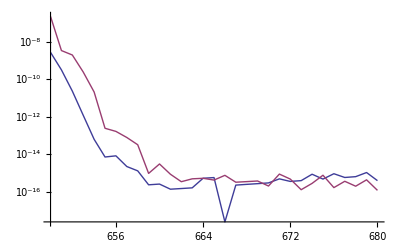

```mathematica
Monitor[TableLogPlot[{err[k],errD[k]},{k,650,680},PlotRange->All],k]
```

## Close

```mathematica
End[]
```